# Tree Size in the Birth-Death-Sampling Model

Some parameters to be used throughout that allow you to separately specify the initial number of infections

```mathematica
parsSIR[i0in_]:={β->2,κ->100,γ->0.5,ψ->0.1,σ->0.01,Τ->10,i0->i0in};
```

```mathematica
MyCol=Table[ColorData["DarkBands"][i/6-0.01],{i,1,6}]
```

{RGBColor[0.23132947583985186, 0.5230171758179645, 0.6762635983204028],RGBColor[0.30222321343557096, 0.5283591583672841, 0.26781478622442834],RGBColor[0.6416497175320824, 0.22039024680361508, 0.2965244160637617],RGBColor[0.6953106517659292, 0.4338224431042085, 0.2550317501625878],RGBColor[0.3208696220556491, 0.33272406933605325, 0.551604665638763],RGBColor[0.8884240140546887, 0.8315410617160953, 0.3918643845410284]}

```mathematica
Dir="/Users/ailenemacpherson/Dropbox/Apps/Overleaf/EpidemiologicalTreeSize/Plots";
```

## Theoretical Background:

## SIR(S) Dynamics

The system of ODEs

```mathematica
f1[t_]:=-β/κ s[t]i[t]+σ r[t]
f2[t_]:=β/κ s[t]i[t]-γ i[t]
f3[t_]:=γ i[t]-σ r[t]
```

The equilibrium

```mathematica
Solve[{f1[t]==0,f2[t]==0,f3[t]==0,s[t]+i[t]+r[t]==κ},{s[t],i[t],r[t]}]
```

{{s[t]→κ,i[t]→0,r[t]→0},{s[t]→(γ κ)/β,i[t]→((β-γ) κ σ)/(β (γ+σ)),r[t]→((β-γ) γ κ)/(β (γ+σ))}}

```mathematica
endemic=((β-γ) κ σ)/(β (γ+σ));
```

```mathematica
Series[endemic,{σ,0,1}]
```

((β-γ) κ σ)/(β γ)+O[σ]^2

Numerical solution

```mathematica
nsol[pars_]:=NDSolve[{D[s[t],t]==f1[t],D[i[t],t]==f2[t],D[r[t],t]==f3[t],s[0]==κ-i0,i[0]==i0,r[0]==0}/.pars,{s[t],i[t],r[t]},{t,0,T/.pars}][[1]]
```

```mathematica
(*SIR*)
parsSIR[i0in_,Tin_]:={β->2,κ->100,γ->0.5,ψ->0,σ->0.0,T->Tin,i0->i0in};
(*SIRS*)
parsSIR2[i0in_,Tin_]:={β->2,κ->100,γ->0.5,ψ->0,σ->0.04,T->Tin,i0->i0in};
```

As shown by Cadoni and Gaeta 2020, a general solution for the SIR model can be obtained through a transformation of time in units of t to units of  as defined by (Cadoni and Gaeta 2020 Equation 3):

```mathematica
arg=1/(κ- (κ-i0) Exp[-β/κ x]-γ x);
```

The duration of the infection in terms of  is given by (Cadoni and Gaeta 2020 Equation 20)

```mathematica
Clear[tMax]
```

```mathematica
τMax[pars_]:=τ/.FindRoot[(κ-i0)(1-Exp[-β/κ τ])-γ τ==0/.pars,{τ,κ/.pars}]
```

```mathematica
τMax[parsSIR[1,20]]
```

193.903

```mathematica
tMax[pars_]:=NIntegrate[arg/.parsSIR[1,20],{x,0,τMax[pars]}]
```

```mathematica
tMax[parsSIR[1,20]]
```

13.1722

The time of the epidemic peak is given by  (Cadoni and Gaeta 2020 Equation 11):

```mathematica
Clear[τStar]
```

```mathematica
τStar[pars_]:=κ/β Log[((κ-i0)β)/(κ γ)]/.pars;
```

```mathematica
τStar[parsSIR[1,20]]
```

68.8122

```mathematica
tStar[pars_]:=NIntegrate[arg/.pars,{x,0,τStar[pars]}]
```

```mathematica
tStar[parsSIR[1,20]]
```

3.87559

The height of the peak is given by  (Cadoni and Gaeta 2020 Equation 8)

```mathematica
Clear[iMax]
```

```mathematica
iStar[pars_]:=κ(1- γ/β-γ/β Log[β/γ])/.pars
```

```mathematica
iStarTilde[R0_]:=(1- 1/R0-1/R0 Log[R0])
```

Harmonic mean population size

```mathematica
NHar[k_,Δt_]:=Block[{t0,t1,nH},
t0=Simplify[Δt(k-1)];
t1=Simplify[Δt k];
nH=1/NIntegrate[Evaluate[1/(i[t]/.nsol[parsSIR[1,50]])/.t->t2],{t2,t0,t1}];
{{t0,nH},{t1,nH}}
]
```

```mathematica
?SwatchLegend
```

```mathematica
plot0[pars_]:=Block[{leg1,leg2,leg3},
leg1=LineLegend[{MyCol[[4]],MyCol[[5]]},{"SIR","SIRS"}];
leg2=LineLegend[{Directive[MyCol[[4]],Dashed],Directive[MyCol[[5]],Dotted],Black,Directive[Dashed,Gray]},{"","","",""}];
leg3=SwatchLegend[{Directive[EdgeForm[{Darker[MyCol[[4]]],Thick}],FaceForm[{Lighter[MyCol[[4]]],Opacity[0.5]}]]},{"SIR "}];
Show[
(*SIR and SIRS dynamics*)
Plot[{Evaluate[i[t]/.nsol[parsSIR[1,T/.pars]]],Evaluate[i[t]/.nsol[parsSIR2[1,T/.pars]]]},{t,0,T/.pars},PlotRange->All,PlotStyle->{MyCol[[4]],Lighter[MyCol[[5]]]}],
(*SIRS Equilibrium*)
Plot[endemic/.parsSIR2[1,T/.pars],{t2,0,T/.pars},PlotStyle->{Lighter[MyCol[[5]]],Dotted},PlotRange->All],
(*Time of peak:tStar and end of epidemic*)
ListLinePlot[{{{tStar[pars],0},{tStar[pars],iStar[pars]*1.1}},{{tMax[pars],0},{tMax[pars],iStar[pars]*1.1}}},PlotStyle->{Black,Directive[Gray,Dashed]}],
(*Height of peak:Istar*)
Plot[iStar[pars],{t,0,T/.pars},PlotStyle->Directive[MyCol[[4]],Dashed]],
(*Harmonic Mean population size*)
ListLinePlot[Table[NHar[k,2],{k,1,25}],PlotStyle->Directive[Lighter[MyCol[[4]]]],PlotRange->All,Filling->Axis],
Frame->True,FrameTicks->{{True,False},{True,False}},FrameStyle->Directive[Black,12],PlotStyle->{Black,LightGray},FrameLabel->{"Time","Number Infected"},
Epilog->{Inset[leg1,Scaled[{0.65,0.55}]],Inset[leg2,Scaled[{0.85,0.5}]],Inset[leg3,Scaled[{0.65,0.4}]]}]]
```

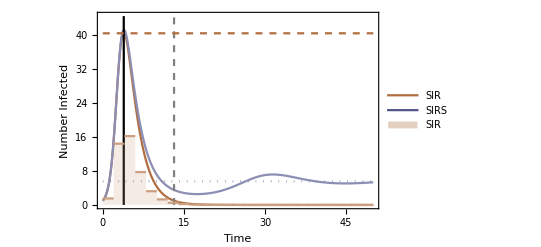

Export::nodir: Directory /Users/ailenemacpherson/Dropbox/Apps/Overleaf/EpidemiologicalTreeSize/Plots/ does not exist.

Export::noopen: Cannot open /Users/ailenemacpherson/Dropbox/Apps/Overleaf/EpidemiologicalTreeSize/Plots/SizePlot1.jpeg.

```mathematica
plot0[parsSIR[1,50]]
Export[Dir<>"/SizePlot1.jpeg",%];
```

## Total outbreak size

Here we calculate the total outbreak is given by:

```mathematica
Clear[size]
```

```mathematica
sizeTot[R0_]:=Select[Rtot/.NSolve[1-Rtot== Exp[-Rtot R0],Rtot],#>0&][[1]]//Quiet
```

## Branching Process: Probability of Extinction

Here we calculate the probability of extinction without being observed of a birth-death-sampling process

```mathematica
Solve[Pext== γ/(β+γ)+β/(β+γ)Pext^2,Pext]
```

{{Pext→1},{Pext→γ/β}}

```mathematica
sol=Solve[Pext== γ/(β+γ+ψ)+β/(β+γ+ψ)Pext^2,Pext]
```

{{Pext→-((β+γ+ψ) (-1-√(1-(4 β γ)/(β+γ+ψ)^2)))/(2 β)},{Pext→-((β+γ+ψ) (-1+√(1-(4 β γ)/(β+γ+ψ)^2)))/(2 β)}}

```mathematica
Simplify[Series[(Pext/.sol[[1]]),{ψ,0,1}],Assumptions->{β>γ>0}]
```

1+ψ/(β-γ)+O[ψ]^2

This is not a valid probability

```mathematica
Simplify[Series[(Pext/.sol[[2]]),{ψ,0,1}],Assumptions->{β>γ>0}]
```

γ/β-(γ ψ)/(β^2-β γ)+O[ψ]^2

Assuming that there are a small number  of infectious individuals the probability of extinction without sampling is approximated by the probability that each of these individuals do not seed an observed outbreak .

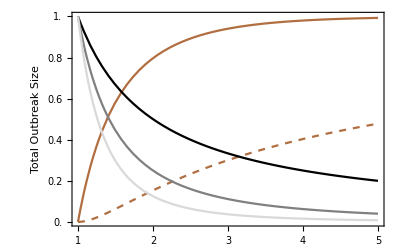

Export::nodir: Directory /Users/ailenemacpherson/Dropbox/Apps/Overleaf/EpidemiologicalTreeSize/Plots/ does not exist.

Export::noopen: Cannot open /Users/ailenemacpherson/Dropbox/Apps/Overleaf/EpidemiologicalTreeSize/Plots/SizePlot2.jpeg.

```mathematica
leg1=LineLegend[{MyCol[[4]],Directive[MyCol[[4]],Dashed]},{" ",""}];
leg2=LineLegend[{Black,Gray,LightGray},{"","",""}];
Plot[{sizeTot[R0],iStarTilde[R0],1/R0,(1/R0)^2,(1/R0)^3},{R0,1,5},PlotStyle->{MyCol[[4]],Directive[MyCol[[4]],Dashed],Black,Gray,LightGray},Frame->True,FrameTicks->{{Table[{x,x},{x,0,1,0.2}],Table[{x,x},{x,0,1,0.2}]},{True,False}},FrameStyle->{{Directive[MyCol[[4]],12],Directive[Black,12]},{Directive[Black,12],Directive[Black,12]}},FrameLabel->{{"Total Outbreak Size",Rotate["Probability",π]},{"",None}},Epilog->{Inset[leg1,Scaled[{0.5,0.7}]],Inset[leg2,Scaled[{0.75,0.7}]]}]
Export[Dir<>"/SizePlot2.jpeg",%];
```

## Stochastic Outbreak Size: Selleke’s Method

```mathematica
Clear[Selleke]
Selleke[pars_,intS_]:=Selleke[pars,intS]=Block[{Qlist,Tlist},
Qlist=Sort[Join[Table[0,{i,1,i0/.pars}],Table[RandomVariate[ExponentialDistribution[1]],{i,i0+1/.pars,κ/.pars}]]];
Tlist=Accumulate[Table[(β/κ/.pars )RandomVariate[ExponentialDistribution[γ/.pars]],{i,1,κ/.pars}]];
FirstPosition[Tlist-Qlist,_?(#<0&)][[1]]
]
```

```mathematica
Clear[SIRSSim]
SIRSSim[pars_,intS_]:=SIRSSim[pars,intS]=Block[{events,rates,out,Δt,e,temp},
events[Δt_]:={(*inf*){Δt,-1,1,0,1},(*rec*){Δt,0,-1,1,0},(*wane*){Δt,1,0,-1,0}};
rates[state_]:={β/κ state[[2]]state[[3]],γ state[[3]],σ state[[4]]}/.pars;
out={{0,κ-i0,i0,0,i0}}/.pars;
temp=rates[out[[-1]]];
Δt=RandomVariate[ExponentialDistribution[Total[temp]]];
While[out[[-1,3]]>0&&(out[[-1,1]]+Δt)<=(T/.pars),
e=RandomChoice[temp->{1,2,3}];
AppendTo[out,out[[-1]]+events[Δt][[e]]];
temp=rates[out[[-1]]];
If[out[[-1,3]]>0,Δt=RandomVariate[ExponentialDistribution[Total[temp]]]];
];
out
]
```

Mean epidemic size across parameter space

```mathematica
sizeTab=Flatten[Table[{R0,γin,N[Mean[Table[SIRSSim[{β->R0 γin,κ->100,γ->γin,ψ->0,σ->0.,T->50,i0->1},intS][[-1,-1]],{intS,1,200}]]]},{R0,1,5,0.25},{γin,0.1,0.5,0.05}],1];
```

```mathematica
ListContourPlot[sizeTab];
```

```mathematica
lm=LinearModelFit[sizeTab,{x,y,x^2,y^2,x y},{x,y}];
```

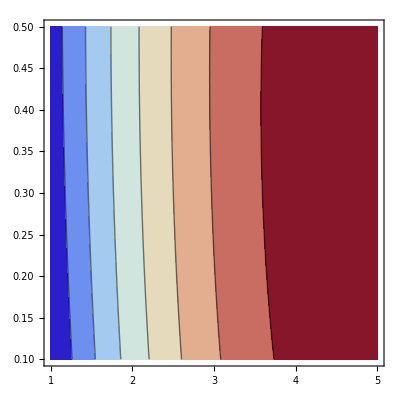

Export::nodir: Directory /Users/ailenemacpherson/Dropbox/Apps/Overleaf/EpidemiologicalTreeSize/Plots/ does not exist.

Export::noopen: Cannot open /Users/ailenemacpherson/Dropbox/Apps/Overleaf/EpidemiologicalTreeSize/Plots/SizePlot3b.jpeg.

```mathematica
MeanSize=ContourPlot[lm[x,y],{x,1,5},{y,0.1,0.5},ColorFunction->ColorData["ThermometerColors"],Frame->True,FrameTicks->{{True,False},{True,False}},FrameStyle->Directive[Black,16],FrameLabel->{"",""}]
Export[Dir<>"/SizePlot3b.jpeg",%];
```

```mathematica
BarLegend[{"ThermometerColors",{Min[sizeTab[[;;,3]]],Max[sizeTab[[;;,3]]]}},LegendLabel->,LabelStyle->Directive[Black, 12]]
Export[Dir<>"SizePlot3bLeg.jpeg",%];
```

Export::nodir: Directory /Users/ailenemacpherson/Dropbox/Apps/Overleaf/EpidemiologicalTreeSize/ does not exist.

Export::noopen: Cannot open /Users/ailenemacpherson/Dropbox/Apps/Overleaf/EpidemiologicalTreeSize/PlotsSizePlot3bLeg.jpeg.

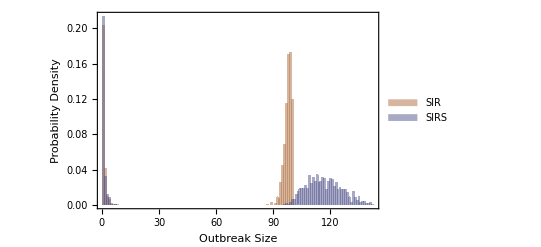

Export::nodir: Directory /Users/ailenemacpherson/Dropbox/Apps/Overleaf/EpidemiologicalTreeSize/Plots/ does not exist.

Export::noopen: Cannot open /Users/ailenemacpherson/Dropbox/Apps/Overleaf/EpidemiologicalTreeSize/Plots/SizePlot3.jpeg.

```mathematica
leg=SwatchLegend[{Directive[MyCol[[4]], Opacity[0.5]],Directive[MyCol[[5]], Opacity[0.5]]},{"SIR","SIRS"}];
Histogram[{
(*SIR Mode*)
Table[SIRSSim[parsSIR[1,20],intS][[-1,-1]],{intS,1,1000}],
(*SIRS Mode*)
Table[SIRSSim[parsSIR2[1,20],intS][[-1,-1]],{intS,1,1000}]},{1},"PDF",ChartStyle->{Directive[MyCol[[4]], Opacity[0.5]],Directive[MyCol[[5]], Opacity[0.5]]},Frame->True,FrameTicks->{{True,False},{True,False}},FrameStyle->Directive[Black,12],FrameLabel->{"Outbreak Size","Probability Density"},
(*Epilog*)
Epilog->Inset[leg,Scaled[{0.8,0.75}]]]
Export[Dir<>"/SizePlot3.jpeg",%];
```

## Deterministic Model

The RHS of the ODEs for the SIR model

```mathematica
f1[t_]:=-β/κ s[t]i[t]+σ r[t]
f2[t_]:=β/κ s[t]i[t]-(γ+ψ)i[t]
f3[t_]:=(γ+ψ)i[t]-σ r[t]
```

### Numerical Solution

```mathematica
Clear[odes]
odes[pars_]:=odes[pars]={D[s[t],t]==f1[t],D[i[t],t]==f2[t],D[r[t],t]==f3[t],s[0]==κ-i0,i[0]==i0,r[0]==0}/.pars
vars={s[t],i[t],r[t]};
Clear[nsol]
nsol[pars_]:=nsol[pars]=NDSolve[odes[pars],vars,{t,0,Τ/.pars}][[1]]
sNSol[pars_,t2_]:=Evaluate[s[t]/.nsol[pars]]/.t->t2
iNSol[pars_,t2_]:=Evaluate[i[t]/.nsol[pars]]/.t->t2
rNSol[pars_,t2_]:=Evaluate[r[t]/.nsol[pars]]/.t->t2
```

```mathematica
iNSol[parsSIR[3],0.3]
```

4.45776

```mathematica
lNSol[pars_,t2_]:=NIntegrate[(ψ/.pars)iNSol[pars,x],{x,0,t2}]
```

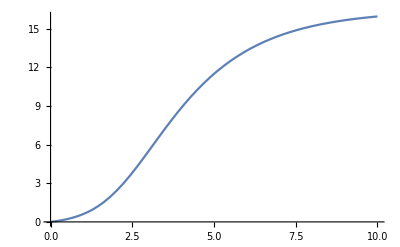

```mathematica
Plot[lNSol[parsSIR[3],x],{x,0,10}]
```

### Equilibrium

```mathematica
equ=Solve[{f1[t]==0,f2[t]==0,f3[t]==0,s[t]+i[t]+r[t]==κ},{s[t],i[t],r[t]}][[2]]
```

{s[t]→(κ (γ+ψ))/β,i[t]→(κ σ (β-γ-ψ))/(β (γ+σ+ψ)),r[t]→(κ (β-γ-ψ) (γ+ψ))/(β (γ+σ+ψ))}

## Stochastic Simulations

## Simulations

```mathematica
Clear[Events]
```

```mathematica
Events[Δt_]:={{Δt,-1,1,0,0},{Δt,0,-1,1,0},{Δt,0,-1,1,1},{Δt,1,0,-1,0}};
Rates[state_]:={β/κ state[[2]]state[[3]],γ state[[3]],ψ state[[3]],σ state[[4]]};
```

```mathematica
Clear[sim]
sim[pars_,intS_]:=sim[pars,intS]=Block[{out,Δt,temp,t,event},
out={{0,κ-i0,i0,0,0}}/.pars;
temp=Rates[out[[-1]]]/.pars;
Δt=RandomVariate[ExponentialDistribution[Total[temp]]];
While[(out[[-1,1]]+Δt&&out[[-1,3]]>0)<(Τ/.pars),
event=RandomChoice[temp->{1,2,3,4}];
AppendTo[out,out[[-1]]+Events[Δt][[event]]];
temp=Rates[out[[-1]]]/.pars;
Δt=RandomVariate[ExponentialDistribution[Total[temp]]];
];
AppendTo[out,Join[{Τ/.pars},out[[-1,2;;]]]];
out
]
```

```mathematica
Clear[simInt]
simInt[pars_,intS_,var_]:=simInt[pars,intS,var]=Interpolation[sim[pars,intS][[;;,{1,var+1}]],InterpolationOrder->0]
```

```mathematica
simInt[parsSIR[3],1,4]
```

InterpolatingFunction[…]

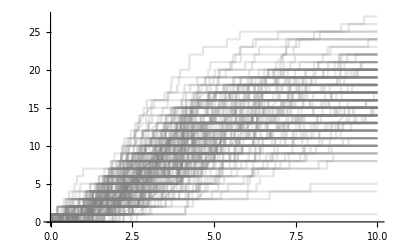

```mathematica
Plot[Evaluate[Table[simInt[parsSIR[5],intS,4][x],{intS,1,200}]],{x,0,Τ/.parsSIR[1]},PlotRange->All,PlotStyle->Directive[Gray,Opacity[0.2]]]
```

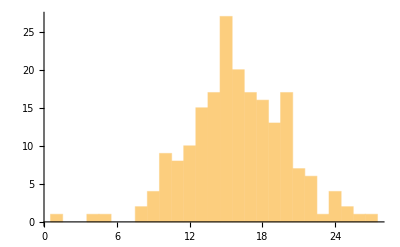

```mathematica
Histogram[Table[simInt[parsSIR[5],intS,4][Τ/.parsSIR[5]],{intS,1,200}]]
```

## Moments

```mathematica
MSim[v_,t2_,pars_]:=Mean[Table[simInt[pars,intS,v][t2],{intS,1,200}]]
VSim[v_,t2_,pars_]:=Variance[Table[simInt[pars,intS,v][t2],{intS,1,200}]]
```

How do the moments compare to the deterministic model? And how does this depend on the initial number of infections?

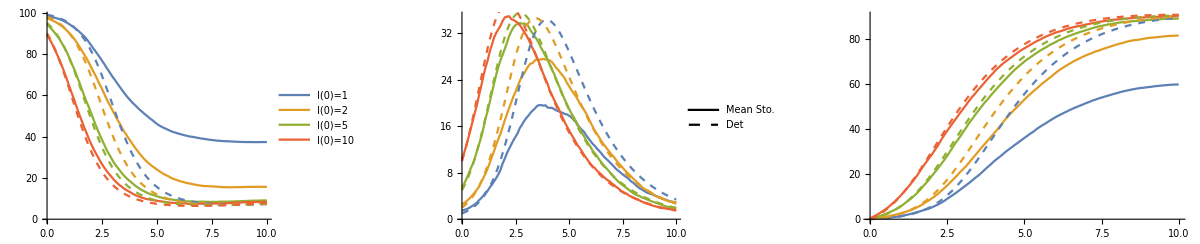

```mathematica
leg1=LineLegend[Table[ColorData[97][x],{x,1,4}],Table["I(0)="<>ToString[i0],{i0,{1,2,5,10}}]];
leg2=LineLegend[{Automatic,Dashed},{"Mean Sto.","Det"}];
GraphicsRow[{
(*Susceptible*)
Show[ListLinePlot[Table[Table[{t2,MSim[1,t2,parsSIR[i0]]},{t2,0,10,0.1}],{i0,{1,2,5,10}}],Epilog->Inset[leg1,Scaled[{0.8,0.8}]]],
Plot[Evaluate[Table[s[t]/.nsol[parsSIR[i0]]/.t->t2,{i0,{1,2,5,10}}]],{t2,0,10},PlotStyle->Dashed]],
(*Infected*)Show[ListLinePlot[Table[Table[{t2,MSim[2,t2,parsSIR[i0]]},{t2,0,10,0.1}],{i0,{1,2,5,10}}],Epilog->Inset[leg2,Scaled[{0.8,0.8}]]],
Plot[Evaluate[Table[i[t]/.nsol[parsSIR[i0]]/.t->t2,{i0,{1,2,5,10}}]],{t2,0,10},PlotStyle->Dashed]],
(*Recovered*)
Show[ListLinePlot[Table[Table[{t2,MSim[3,t2,parsSIR[i0]]},{t2,0,10,0.1}],{i0,{1,2,5,10}}]],
Plot[Evaluate[Table[r[t]/.nsol[parsSIR[i0]]/.t->t2,{i0,{1,2,5,10}}]],{t2,0,10},PlotStyle->Dashed]]},ImageSize->Full]
```

## Ensemble Moment Approximation

## Equations

The stochastic process

```mathematica
Δe={{-1,1,0,0},{0,-1,1,0},{0,-1,1,1},{1,0,-1,0}};
rates={β/κ s i,γ i,ψ i,σ r};
var={s,i,r,l};
par={β,ψ,γ,σ};
inits={κ-i0,i0,0,0};
```

Substitutions that take the expectation of an expression in terms of the non-centered moments

```mathematica
μSub=Table[var[[v]]->μ[ToString[var[[v]]],t],{v,1,4}];
νSub=Flatten[Table[var[[v1]]var[[v2]]->ν[ToString[var[[v1]]],ToString[var[[v2]]],t],{v1,1,4},{v2,v1,4}]];
χSub=Flatten[Table[var[[v1]]var[[v2]]var[[v3]]->χ[ToString[var[[v1]]],ToString[var[[v2]]],ToString[var[[v3]]],t],{v1,1,4},{v2,v1,4},{v3,v2,4}]];
ηSub=Flatten[Table[var[[v1]]var[[v2]]var[[v3]]var[[v4]]->η[ToString[var[[v1]]],ToString[var[[v2]]],ToString[var[[v3]]],ToString[var[[v4]]],t],{v1,1,4},{v2,v1,4},{v3,v2,4},{v4,v3,4}]];
```

The non-centered odes and variables

```mathematica
(*A list of the state variables*)
μVars=μSub[[;;,2]];νVars=νSub[[;;,2]];χVars=χSub[[;;,2]];ηVars=ηSub[[;;,2]];
```

```mathematica
μEqus=Table[D[μ[ToString[var[[v]]],t],t]->Collect[Expand[Total[rates*((var[[v]]+Δe[[;;,v]])-var[[v]])]],par]/.ηSub/.χSub/.νSub/.μSub,{v,1,4}];
```

```mathematica
νEqus=Flatten[Table[D[ν[ToString[var[[v1]]],ToString[var[[v2]]],t],t]->Collect[Expand[Total[rates*((var[[v1]]+Δe[[;;,v1]])(var[[v2]]+Δe[[;;,v2]])-var[[v1]]var[[v2]])]],par]/.ηSub/.χSub/.νSub/.μSub,{v1,1,4},{v2,v1,4}]];
```

```mathematica
χEqus=Flatten[Table[D[χ[ToString[var[[v1]]],ToString[var[[v2]]],ToString[var[[v3]]],t],t]->Collect[Expand[Total[rates*((var[[v1]]+Δe[[;;,v1]])(var[[v2]]+Δe[[;;,v2]])(var[[v3]]+Δe[[;;,v3]])-var[[v1]]var[[v2]]var[[v3]])]],par]/.ηSub/.χSub/.νSub/.μSub,{v1,1,4},{v2,v1,4},{v3,v2,4}]];
```

The centered moments

```mathematica
MSub=Table[μ[ToString[var[[v]]],t]->M[ToString[var[[v]]],t],{v,1,4}];
```

```mathematica
MSub
```

{μ[s,t]→M[s,t],μ[i,t]→M[i,t],μ[r,t]→M[r,t],μ[l,t]→M[l,t]}

```mathematica
VSub=Flatten[Table[Solve[(Expand[(var[[v1]]-μVars[[v1]])(var[[v2]]-μVars[[v2]])]/.χSub/.νSub/.μSub)==V[ToString[var[[v1]]],ToString[var[[v2]]],t],ν[ToString[var[[v1]]],ToString[var[[v2]]],t]][[1]],{v1,1,4},{v2,v1,4}]]/.MSub;
```

```mathematica
TSub=Flatten[Table[Solve[(Expand[(var[[v1]]-μVars[[v1]])(var[[v2]]-μVars[[v2]])(var[[v3]]-μVars[[v3]])]/.χSub/.νSub/.μSub)==T[ToString[var[[v1]]],ToString[var[[v2]]],ToString[var[[v3]]],t],χ[ToString[var[[v1]]],ToString[var[[v2]]],ToString[var[[v3]]],t]],{v1,1,4},{v2,v1,4},{v3,v2,4}]]/.VSub/.MSub;
```

```mathematica
FSub=Flatten[Table[Solve[(Expand[(var[[v1]]-μVars[[v1]])(var[[v2]]-μVars[[v2]])(var[[v3]]-μVars[[v3]])(var[[v4]]-μVars[[v4]])]/.ηSub/.χSub/.νSub/.μSub)==F[ToString[var[[v1]]],ToString[var[[v2]]],ToString[var[[v3]]],ToString[var[[v4]]],t],η[ToString[var[[v1]]],ToString[var[[v2]]],ToString[var[[v3]]],ToString[var[[v4]]],t]],{v1,1,4},{v2,v1,4},{v3,v2,4},{v4,v3,4}]]/.TSub/.VSub/.MSub;
```

The variables for the centered moments

```mathematica
MVars=Table[M[ToString[var[[v]]],t],{v,1,4}];
VVars=Flatten[Table[V[ToString[var[[v1]]],ToString[var[[v2]]],t],{v1,1,4},{v2,v1,4}]];
TVars=Flatten[Table[T[ToString[var[[v1]]],ToString[var[[v2]]],ToString[var[[v3]]],t],{v1,1,4},{v2,v1,4},{v3,v2,4}]];
```

The ODEs for the centered moments

```mathematica
MODEs=Table[D[M[ToString[var[[v]]],t],t]==(D[(var[[v]]/.χSub/.νSub/.μSub),t]/.νEqus/.μEqus/.TSub/.VSub/.MSub),{v,1,4}];
```

```mathematica
VODEs=Flatten[Table[D[V[ToString[var[[v1]]],ToString[var[[v2]]],t],t]==(D[(Expand[(var[[v1]]-μVars[[v1]])(var[[v2]]-μVars[[v2]])]/.χSub/.νSub/.μSub),t]/.νEqus/.μEqus/.TSub/.VSub/.MSub),{v1,1,4},{v2,v1,4}]];
```

```mathematica
TODEs=Flatten[Table[D[T[ToString[var[[v1]]],ToString[var[[v2]]],ToString[var[[v3]]],t],t]==(D[(Expand[(var[[v1]]-μVars[[v1]])(var[[v2]]-μVars[[v2]])(var[[v3]]-μVars[[v3]])]/.ηSub/.χSub/.νSub/.μSub),t]/.χEqus/.νEqus/.μEqus/.FSub/.TSub/.VSub/.MSub),{v1,1,4},{v2,v1,4},{v3,v2,4}]];
```

Initial Conditions

```mathematica
MInits=Table[M[ToString[var[[v]]],0]==inits[[v]],{v,1,4}];
VInits=Flatten[Table[V[ToString[var[[v1]]],ToString[var[[v2]]],0]==0,{v1,1,4},{v2,v1,4}]];
TInits=Flatten[Table[T[ToString[var[[v1]]],ToString[var[[v2]]],ToString[var[[v3]]],0]==0,{v1,1,4},{v2,v1,4},{v3,v2,4}]];
```

```mathematica
MInitsSub=Table[M[ToString[var[[v]]],0]->inits[[v]],{v,1,4}];
VInitsSub=Flatten[Table[V[ToString[var[[v1]]],ToString[var[[v2]]],0]->0,{v1,1,4},{v2,v1,4}]];
TInitsSub=Flatten[Table[T[ToString[var[[v1]]],ToString[var[[v2]]],ToString[var[[v3]]],0]->0,{v1,1,4},{v2,v1,4},{v3,v2,4}]];
```

Moment Closure Assumptions

```mathematica
CloseureT=Table[T[ToString[var[[v1]]],ToString[var[[v2]]],ToString[var[[v3]]],t]->0,{v1,1,4},{v2,v1,4},{v3,v2,4}]//Flatten;
```

```mathematica
CloseureF=Table[F[ToString[var[[v1]]],ToString[var[[v2]]],ToString[var[[v3]]],ToString[var[[v4]]],t]->0,{v1,1,4},{v2,v1,4},{v3,v2,4},{v4,v3,4}]//Flatten;
```

```mathematica
TODEs/.CloseureF/.t->0/.MInitsSub/.VInitsSub/.TInitsSub/.parsSIR[1]
```

{T^(0,0,0,1)[s,s,s,0]==-99/50,T^(0,0,0,1)[s,s,i,0]==1.98,T^(0,0,0,1)[s,s,r,0]==9.09495×10^-13,T^(0,0,0,1)[s,s,l,0]==0,T^(0,0,0,1)[s,i,i,0]==-1.98,T^(0,0,0,1)[s,i,r,0]==0.,T^(0,0,0,1)[s,i,l,0]==0.,T^(0,0,0,1)[s,r,r,0]==0.,T^(0,0,0,1)[s,r,l,0]==0,T^(0,0,0,1)[s,l,l,0]==0,T^(0,0,0,1)[i,i,i,0]==1.38,T^(0,0,0,1)[i,i,r,0]==0.6,T^(0,0,0,1)[i,i,l,0]==0.1,T^(0,0,0,1)[i,r,r,0]==-0.6,T^(0,0,0,1)[i,r,l,0]==-0.1,T^(0,0,0,1)[i,l,l,0]==-0.1,T^(0,0,0,1)[r,r,r,0]==0.6,T^(0,0,0,1)[r,r,l,0]==0.1,T^(0,0,0,1)[r,l,l,0]==0.1,T^(0,0,0,1)[l,l,l,0]==0.1}

## Numerical Solution

### Mean Only

```mathematica
Clear[equsAll]
equsAll[pars_]:=equsAll[pars]=Join[MODEs,VODEs,(*TODEs,*)MInits,VInits(*,TInits*)]/.CloseureT/.pars
varsAll=Join[MVars,VVars(*,TVars*)];
```

```mathematica
equsAll[parsSIR[1]]//Length
varsAll//Length
```

28

14

```mathematica
Clear[EMNSol]
EMNSol[pars_]:=EMNSol[pars]=NDSolve[equsAll[pars],varsAll,{t,0,Τ/.pars}][[1]];
```

```mathematica
leg=LineLegend[Table[Directive[{Thick,MyCol[[i]]}],{i,1,4}],{"Ensamble Moment","Deterministic","Mean Stochastic"}];
```

```mathematica
plotDyn[pars_]:=Block[{},
iNSol[pars,0.3];
Plot[{Evaluate[M["i",t]/.EMNSol[pars]],MSim[2,t,pars],iNSol[pars,t]},{t,0,Τ/.pars},PlotStyle->{MyCol[[1]],MyCol[[3]],Black}]]
```

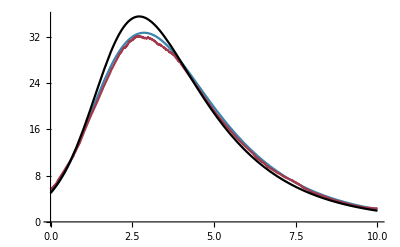

```mathematica
plotDyn[parsSIR[5]]
```

#### Distribution of Tree Sizes

```mathematica
Clear[nSampEM]
nSampEM[pars_]:=Evaluate[M["l",t]/.EMNSol[pars]]/.t->Τ/.pars
```

```mathematica
Clear[nSampDet]
nSampDet[pars_]:=NIntegrate[Evaluate[s[t]/.nsol[pars]],{t,0,10}]*ψ/.pars
```

```mathematica
MyCol
```

{RGBColor[0.23132947583985186, 0.5230171758179645, 0.6762635983204028],RGBColor[0.30222321343557096, 0.5283591583672841, 0.26781478622442834],RGBColor[0.6416497175320824, 0.22039024680361508, 0.2965244160637617],RGBColor[0.6953106517659292, 0.4338224431042085, 0.2550317501625878],RGBColor[0.3208696220556491, 0.33272406933605325, 0.551604665638763],RGBColor[0.8884240140546887, 0.8315410617160953, 0.3918643845410284]}

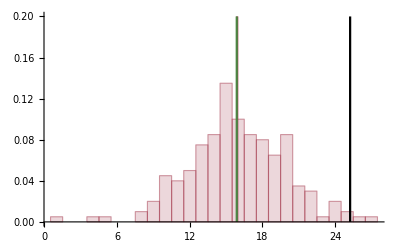

```mathematica
temp=Table[simInt[parsSIR[5],intS,4][Τ/.parsSIR[5]],{intS,1,200}];
Show[
(*Simulation Data*)
Histogram[temp,{1},"Probability",ChartStyle->Directive[{MyCol[[3]],Opacity[0.2]}]],
ListLinePlot[{{Mean[temp],0},{Mean[temp],0.2}},PlotStyle->MyCol[[3]]],
(*Ensemble Moment*)
ListLinePlot[{{nSampEM[parsSIR[5]],0},{nSampEM[parsSIR[5]],0.2}},PlotStyle->MyCol[[2]]],
(*Deterministic*)
ListLinePlot[{{nSampDet[parsSIR[5]],0},{nSampDet[parsSIR[5]],0.2}},PlotStyle->Black]]
```

### Mean and Variance

```mathematica
Clear[equsAll]
equsAll[pars_]:=equsAll[pars]=Join[MODEs,VODEs,TODEs,MInits,VInits,TInits]/.CloseureF/.pars
varsAll=Join[MVars,VVars,TVars];
```

```mathematica
equsAll[parsSIR[1]]//Length
varsAll//Length
```

68

34

```mathematica
Clear[EMNSol]
EMNSol[pars_]:=EMNSol[pars]=NDSolve[equsAll[pars],varsAll,{t,0,Τ/.pars}][[1]];
```

```mathematica
EMNSol[parsSIR[2]];
```

#### Mean Comparison

```mathematica
plotDyn[pars_]:=Block[{},
iNSol[pars,0.3];
Plot[{Evaluate[M["l",t]/.EMNSol[pars]]/.t->x,MSim[4,x,pars],lNSol[pars,x]},{x,0,Τ/.pars},PlotStyle->{MyCol[[2]],MyCol[[3]],{Black,Dashed}},Frame->True,FrameTicks->{{True,False},{True,False}},FrameStyle->Directive[Black,12]]]
```

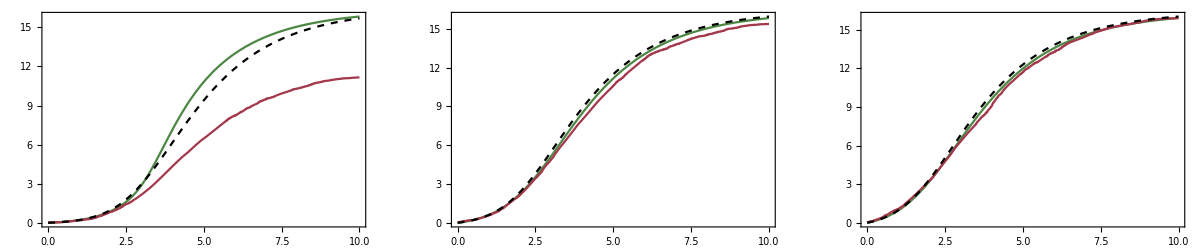

```mathematica
GraphicsRow[{plotDyn[parsSIR[1]],plotDyn[parsSIR[3]],plotDyn[parsSIR[5]]}]
```

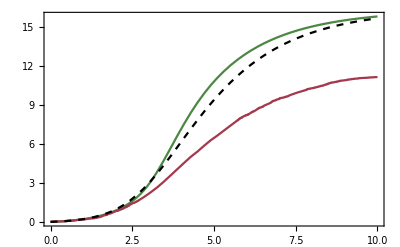

Export::nodir: Directory /Users/ailenemacpherson/Dropbox/Apps/Overleaf/EpidemiologicalTreeSize/Plots/ does not exist.

Export::noopen: Cannot open /Users/ailenemacpherson/Dropbox/Apps/Overleaf/EpidemiologicalTreeSize/Plots/DynPlotSIR1.jpeg.

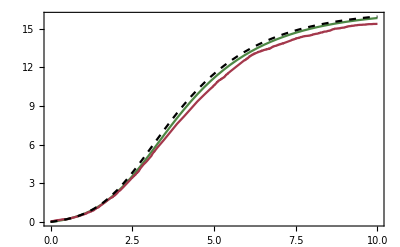

Export::nodir: Directory /Users/ailenemacpherson/Dropbox/Apps/Overleaf/EpidemiologicalTreeSize/Plots/ does not exist.

Export::noopen: Cannot open /Users/ailenemacpherson/Dropbox/Apps/Overleaf/EpidemiologicalTreeSize/Plots/DynPlotSIR3.jpeg.

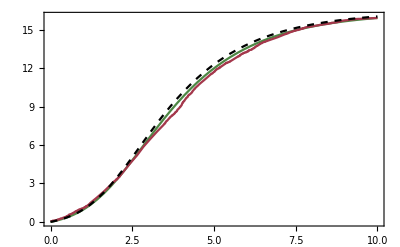

Export::nodir: Directory /Users/ailenemacpherson/Dropbox/Apps/Overleaf/EpidemiologicalTreeSize/Plots/ does not exist.

General::stop: Further output of Export::nodir will be suppressed during this calculation.

Export::noopen: Cannot open /Users/ailenemacpherson/Dropbox/Apps/Overleaf/EpidemiologicalTreeSize/Plots/DynPlotSIR5.jpeg.

General::stop: Further output of Export::noopen will be suppressed during this calculation.

```mathematica
Do[Print[plotDyn[parsSIR[nn]]];
Export[Dir<>"/DynPlotSIR"<>ToString[nn]<>".jpeg",plotDyn[parsSIR[nn]]];,{nn,{1,3,5}}]
```

```mathematica
nSampDet[parsSIR[1]]
```

36.0809

#### Number of Samples Comparison

```mathematica
Clear[nSampEM]
nSampEM[pars_]:=Evaluate[M["l",t]/.EMNSol[pars]]/.t->Τ/.pars
```

```mathematica
nSampVarEM[pars_]:=Evaluate[V["l","l",t]/.EMNSol[pars]]/.t->Τ/.pars
```

```mathematica
Clear[nSampDistEM]
nSampDistEM[pars_]:=nSampDistEM[pars]=NormalDistribution[nSampEM[pars],Sqrt[nSampVarEM[pars]]]
```

```mathematica
Clear[nSampDet]
nSampDet[pars_]:=NIntegrate[Evaluate[i[t]/.nsol[pars]],{t,0,10}]*ψ/.pars
```

```mathematica
plotSIR1[pars_,nMax_,yMax_]:=Block[{temp,nSims},
nSims=1000;
temp=Table[simInt[pars,intS,4][Τ/.pars],{intS,1,nSims}];
Show[
(*Simulation Data*)
Histogram[temp,{1},"PDF",ChartStyle->Directive[{MyCol[[3]],Opacity[0.2]}]],
ListLinePlot[{{Mean[temp],0},{Mean[temp],yMax}},PlotStyle->MyCol[[3]]],
(*Ensemble Moment*)
ListLinePlot[{{nSampEM[pars],0},{nSampEM[pars],yMax}},PlotStyle->{MyCol[[2]],Dashed}],
Plot[PDF[nSampDistEM[pars],x],{x,0,30},PlotStyle->MyCol[[2]],Filling->Axis,FillingStyle->Directive[MyCol[[2]],Opacity[0.2]]],
(*Deterministic*)
ListLinePlot[{{nSampDet[pars],0},{nSampDet[pars],yMax}},PlotStyle->Black],PlotRange->{{-0.01,nMax},{0,yMax}},Frame->True,FrameTicks->{{True,False},{True,False}},FrameStyle->Directive[Black,12],FrameLabel->{"Observed Tree Size","Probability Density"}]]
```

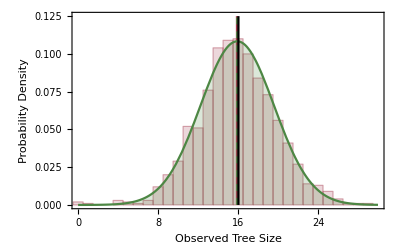

Export::nodir: Directory /Users/ailenemacpherson/Dropbox/Apps/Overleaf/EpidemiologicalTreeSize/Plots/ does not exist.

Export::noopen: Cannot open /Users/ailenemacpherson/Dropbox/Apps/Overleaf/EpidemiologicalTreeSize/Plots/nDistSIR.jpeg.

```mathematica
plotSIR1[parsSIR[5],30,0.125]
Export[Dir<>"/nDistSIR.jpeg",%];
```

```mathematica
leg=LineLegend[{MyCol[[3]],{MyCol[[3]],Dashed},Black,(*{MyCol[[1]],Dashed},*)MyCol[[2]]},{"Simulation All","Simulation Extant","Deterministic",(*"Master Equation",*)"Ensemble Moment"},LegendLabel->Style["Means",16,Bold]];
leg2=SwatchLegend[{Directive[MyCol[[3]],Opacity[0.4]],(*Black,*)(*Directive[MyCol[[1]],Opacity[0.4]],*)Directive[MyCol[[2]],Opacity[0.4]]},{"Simulation",(*"Deterministic",*)(*"Master Equation",*)"Ensemble Moment"},LegendLabel->Style["Distributions",16,Bold]];
GraphicsRow[{leg2,leg}]
Export[Dir<>"/DynPlotSIRLeg.jpeg",%];
```

-Graphics-

Export::nodir: Directory /Users/ailenemacpherson/Dropbox/Apps/Overleaf/EpidemiologicalTreeSize/Plots/ does not exist.

Export::noopen: Cannot open /Users/ailenemacpherson/Dropbox/Apps/Overleaf/EpidemiologicalTreeSize/Plots/DynPlotSIRLeg.jpeg.

## Epidemiological Determinants of Tree Size

```mathematica
parsSIR2[i0in_,R0_,g_]:=Block[{temp,βin},
temp={β->"NA",κ->200,γ->g,ψ->0.1,σ->0.01,Τ->10,i0->i0in};
βin=R0*(γ+ψ)/.temp;
{β->βin,κ->200,γ->g,ψ->0.1,σ->0.01,Τ->10,i0->i0in}
];
```

```mathematica
parsTest0:={β->0.2,γ->0.01,ψ->0.01,σ->0.001,κ->300, tMax->100,i0->i01, ρ ->0};
```

```mathematica
parsSIR2[i0in_,R0_,g_]:=Block[{temp,βin},
temp={β->"NA",κ->300,γ->g,ψ->0.01,σ->0.001,Τ->100,i0->i0in};
βin=R0*(γ+ψ)/.temp;
{β->βin,κ->300,γ->g,ψ->0.01,σ->0.001,Τ->100,i0->i0in}
];
```

```mathematica
Clear[nInfDet]
nInfDet[pars_]:=NIntegrate[Evaluate[i[t]/.nsol[pars]],{t,0,10}]
```

```mathematica
plot1=ListContourPlot[Flatten[Table[{R0,γ,nSampDet[parsSIR2[5,R0,γ]]},{R0,1,5,0.25},{γ,0,0.5,0.05}],1],Contours->Table[x,{x,5,50,5}],ContourShading->None,ContourStyle->Table[Directive[Dashed,Thick,ColorData["RedBlueTones"][(10-c)/10],Opacity[1]],{c,1,10}]];
```

```mathematica
plot2=ListContourPlot[Flatten[Table[{R0,γ,nSampEM[parsSIR2[5,R0,γ]]},{R0,1,5,0.25},{γ,0,0.5,0.05}],1],Contours->Table[x,{x,5,50,5}],ContourShading->None,ContourStyle->Table[Directive[Thick,ColorData["RedBlueTones"][(10-c)/10],Opacity[1]],{c,1,10}]];
```

The EM and Deterministic models give very similar estimates of the expected number of samples.

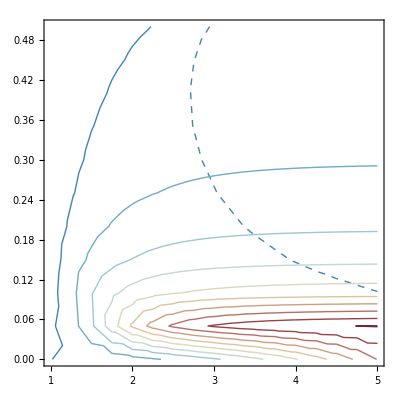

```mathematica
Show[plot1,plot2]
```

Below we show the mean and CV of the number of samples

```mathematica
tab3=Flatten[Table[{R0,γ,nSampEM[parsSIR2[5,R0,γ]]},{R0,1,5,0.25},{γ,0.05,0.5,0.05}],1];
plot3=ListContourPlot[tab3,Contours->Table[x,{x,10,50,5}],ContourShading->Table[Directive[Opacity[0.1],ColorData["RedBlueTones"][(10-c)/10],Opacity[1]],{c,1,10}],ContourStyle->Table[Directive[Thick,ColorData["RedBlueTones"][(10-c)/10],Opacity[1]],{c,1,10}],FrameTicks->{{True,False},{True,False}},FrameStyle->Directive[Black,12]];
```

```mathematica
tab4=Flatten[Table[{R0,γ,Sqrt[nSampVarEM[parsSIR2[5,R0,γ]]]/nSampEM[parsSIR2[5,R0,γ]]},{R0,1,5,0.25},{γ,0.05,0.5,0.05}],1];
plot4=ListContourPlot[tab4,Contours->Table[x,{x,0.2,1,0.1}],ContourStyle->Table[Directive[Thick,ColorData["RedBlueTones"][(10-c)/10],Opacity[1]],{c,1,10}],ContourShading->Table[Directive[Opacity[0.1],ColorData["RedBlueTones"][(10-c)/10],Opacity[1]],{c,1,10}],FrameTicks->{{True,False},{True,False}},FrameStyle->Directive[Black,12]];
```

Sampling fraction

```mathematica
Solve[f==ψ/(ψ+γ),ψ]//Simplify
```

{{ψ→-(f γ)/(-1+f)}}

```mathematica
(*Constant Sampling Fraction*)
parsSIR3[i0in_,R0_,g_,f_]:=Block[{temp,βin},
temp={β->"NA",κ->200,γ->g,ψ->(f g)/(1-f),σ->0.01,Τ->10,i0->i0in};
βin=R0*(γ+ψ)/.temp;
{β->βin,κ->200,γ->g,ψ->(f g)/(1-f),σ->0.01,Τ->10,i0->i0in}
];
```

```mathematica
parsSIR3[i0in_,R0_,g_,f_]:=Block[{temp,βin},
temp={β->"NA",κ->300,γ->g,ψ->(f g)/(1-f),σ->0.001,Τ->100,i0->i0in};
βin=R0*(γ+ψ)/.temp;
{β->βin,κ->300,γ->g,ψ->(f g)/(1-f),σ->0.001,Τ->100,i0->i0in}
];
```

```mathematica
parsSIR3[5,5,0.4,0.2]
```

{β→2.5,κ→300,γ→0.4,ψ→0.1,σ→0.001,Τ→100,i0→5}

```mathematica
nSampEM[parsSIR3[5,R0,γ,0.2]]
```

ReplaceAll::reps: {M^(0,1)[s,t]==0.001 M[r,t]-0.00416667 R0 γ (M[i,t] M[s,t]+V[s,i,t]),M^(0,1)[i,t]==-1.25 γ M[i,t]+0.00416667 R0 γ (M[i,t] M[s,t]+V[s,i,t]),«8»,«58»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {M^(0,1)[s,Τ]==0.001 M[r,Τ]-0.00416667 R0 γ (M[i,Τ] M[s,Τ]+V[s,i,Τ]),M^(0,1)[i,Τ]==-1.25 γ M[i,Τ]+0.00416667 R0 γ (M[i,Τ] M[s,Τ]+V[s,i,Τ]),«8»,«58»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {M^(0,1)[s,100]==0.001 M[r,100]-0.00416667 R0 γ (M[i,100] M[s,100]+V[s,i,100]),«9»,«58»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
tab5=Flatten[Table[{R0,γ,nSampEM[parsSIR3[5,R0,γ,0.25]]},{R0,1,5,0.25},{γ,0.05,0.5,0.05}],1];
plot5=ListContourPlot[tab5,Contours->Table[x,{x,10,50,5}],ContourShading->Table[Directive[Opacity[0.1],ColorData["RedBlueTones"][(10-c)/10],Opacity[1]],{c,1,10}],ContourStyle->Table[Directive[Thick,ColorData["RedBlueTones"][(10-c)/10],Opacity[1]],{c,1,10}],FrameTicks->{{True,False},{True,False}},FrameStyle->Directive[Black,12]];
```

```mathematica
tab6=Flatten[Table[{R0,γ,Sqrt[nSampVarEM[parsSIR3[5,R0,γ,0.25]]]/nSampEM[parsSIR3[5,R0,γ,0.25]]},{R0,1,5,0.25},{γ,0.05,0.5,0.05}],1];
plot6=ListContourPlot[tab6,Contours->Table[x,{x,0.2,1,0.1}],ContourStyle->None,ContourShading->Table[Directive[Opacity[1],ColorData["RedBlueTones"][(10-c)/10]],{c,1,10}],FrameTicks->{{True,False},{True,False}},FrameStyle->Directive[Black,12]];
```

```mathematica
PtA={1.5,0.1};PtB={3,0.25};PtC={4.5,0.45};
```

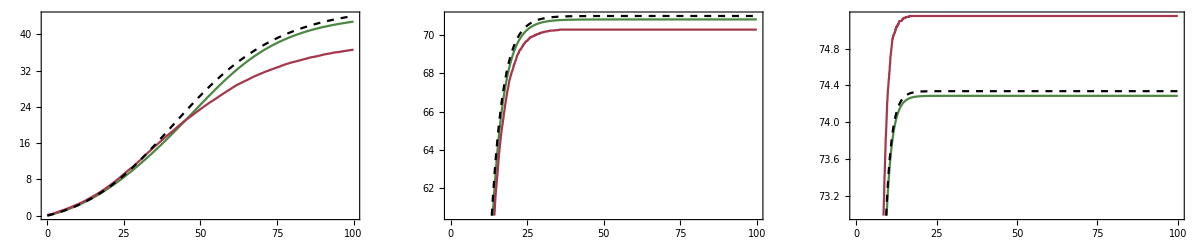

```mathematica
GraphicsRow[{plotDyn[parsSIR3[5,PtA[[1]],PtA[[2]],0.25]],plotDyn[parsSIR3[5,PtB[[1]],PtB[[2]],0.25]],plotDyn[parsSIR3[5,PtC[[1]],PtC[[2]],0.25]]}]
```

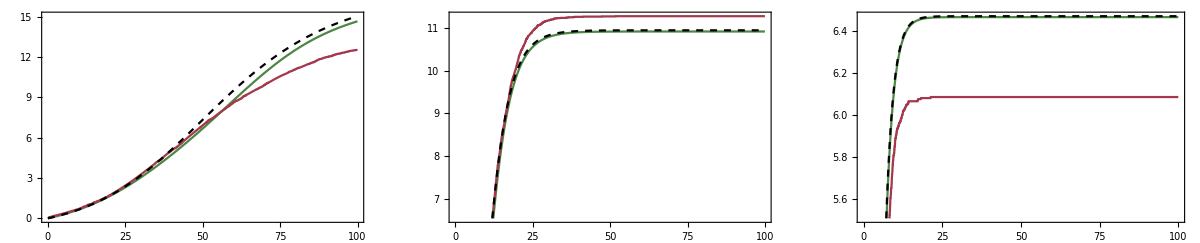

```mathematica
GraphicsRow[{plotDyn[parsSIR2[5,PtA[[1]],PtA[[2]]]],plotDyn[parsSIR2[5,PtB[[1]],PtB[[2]]]],plotDyn[parsSIR2[5,PtC[[1]],PtC[[2]]]]}]
```

```mathematica
leg=LineLegend[{MyCol[[3]],{Black,Dashed},MyCol[[2]]},{"Simulation","Deterministic","Ensemble Moment"}];
```

```mathematica
Export[Dir<>"/DynPlotSIR_A.jpeg",plotDyn[parsSIR2[5,PtA[[1]],PtA[[2]]]]];
Export[Dir<>"/DynPlotSIR_B.jpeg",plotDyn[parsSIR2[5,PtB[[1]],PtB[[2]]]]];
Export[Dir<>"/DynPlotSIR_C.jpeg",Show[plotDyn[parsSIR2[5,PtC[[1]],PtC[[2]]]],Epilog->Inset[leg,{8,10}]]];
```

```mathematica
PtA
```

{1.5,0.05}

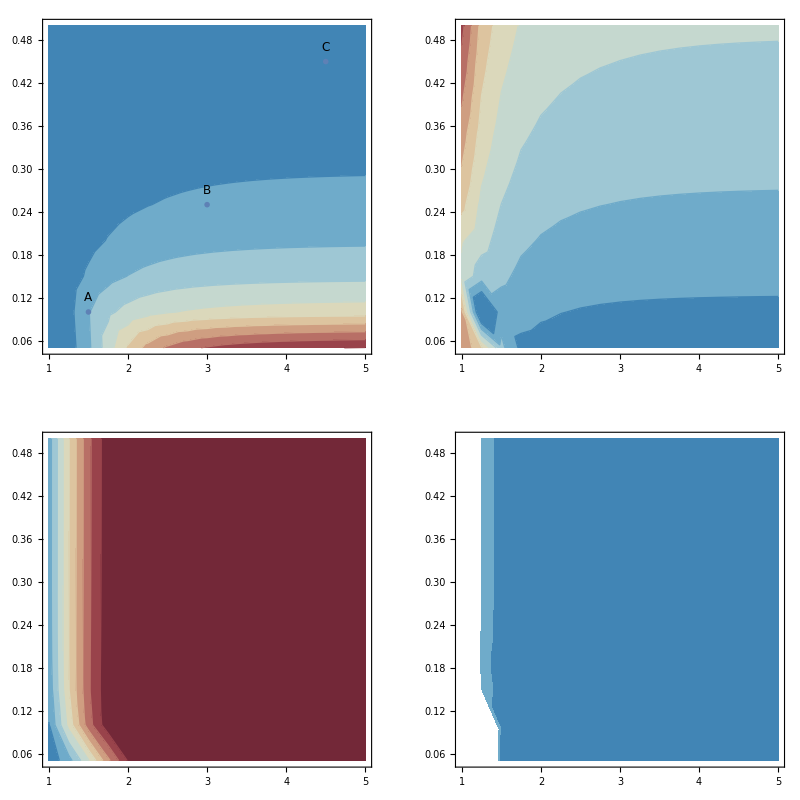

Export::nodir: Directory /Users/ailenemacpherson/Dropbox/Apps/Overleaf/EpidemiologicalTreeSize/Plots/ does not exist.

Export::noopen: Cannot open /Users/ailenemacpherson/Dropbox/Apps/Overleaf/EpidemiologicalTreeSize/Plots/SIRMeanCV.jpeg.

```mathematica
GraphicsGrid[{{Show[plot3,ListPlot[{PtA,PtB,PtC},PlotMarkers->{Black, Medium}],Epilog->Table[Inset[Style[x,12],ToExpression["Pt"<>x]+{0,0.02}],{x,{"A","B","C"}}]],plot4},{plot5,plot6}}]
Export[Dir<>"/SIRMeanCV.jpeg",%];
```

```mathematica
?BarLegend
```

```mathematica
BarLegend[{Table[Directive[Opacity[1],ColorData["RedBlueTones"][(10-c)/10]],{c,0,11}],{10,50}},LegendLayout->"Row",LabelStyle->Directive[Black, Medium](*,Ticks->Table[ToString[i/100]<>"κ",{i,10,50,10}]*),"Ticks"->Table[i,{i,10,50,10}],"TickLabels"->Table[ToString[i/100//N]<>"κ",{i,10,50,10}]]
Export[Dir<>"/SIRMeanCV_Leg1.jpeg",%];
```

Export::nodir: Directory /Users/ailenemacpherson/Dropbox/Apps/Overleaf/EpidemiologicalTreeSize/Plots/ does not exist.

Export::noopen: Cannot open /Users/ailenemacpherson/Dropbox/Apps/Overleaf/EpidemiologicalTreeSize/Plots/SIRMeanCV_Leg1.jpeg.

```mathematica
BarLegend[{Table[Directive[Opacity[1],ColorData["RedBlueTones"][(10-c)/10]],{c,0,11}],{0.2,1}},LegendLayout->"Row",LabelStyle->Directive[Black, Medium]]
Export[Dir<>"/SIRMeanCV_Leg2.jpeg",%];
```

Export::nodir: Directory /Users/ailenemacpherson/Dropbox/Apps/Overleaf/EpidemiologicalTreeSize/Plots/ does not exist.

Export::noopen: Cannot open /Users/ailenemacpherson/Dropbox/Apps/Overleaf/EpidemiologicalTreeSize/Plots/SIRMeanCV_Leg2.jpeg.

```mathematica
PtA={1.5,0.1};PtB={3,0.25};PtC={4.5,0.45};
```

```mathematica
nSampEM[parsSIR2[5,PtB[[1]],PtB[[2]]]]
```

39.2435

```mathematica
Sqrt[nSampVarEM[parsSIR2[5,PtB[[1]],PtB[[2]]]]]/nSampEM[parsSIR2[5,PtB[[1]],PtB[[2]]]]
```

0.151725